## Тест 1

#### Численное решение

```mathematica
ClearAll["Global`*"]
NotebookDirectory[];
n = 2;
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Scheme_cross.txt"]],Table[Real,n+1]];
```

```mathematica
ListPlot3D[plots, PlotRange->All, AxesLabel->Automatic, ColorFunction->"Rainbow"]
```

-Graphics3D-

#### Точное решение

```mathematica
Plot3D[Sin[π x]Cos[π t],{x,0,2},{t,0,1}, ColorFunction->"Rainbow"]
```

-Graphics3D-

#### Эволюция во времени

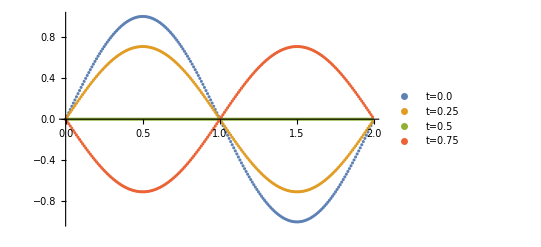

```mathematica
L=2.0;h=0.01;n=L/h;τ=0.01;
ListPlot[{plots⟦1;;n,2;;3⟧,plots⟦1+(n+1)*0.25/τ;;n+(n+1)*0.25/τ,2;;3⟧,plots⟦1+(n+1)*0.5/τ;;n+(n+1)*0.5/τ,2;;3⟧,plots⟦1+(n+1)*0.75/τ;;n+(n+1)*0.75/τ,2;;3⟧},PlotLegends->{"t=0.0","t=0.25","t=0.5","t=0.75"},PlotRange->All]
```

## Тест 2

#### Численное решение

```mathematica
ClearAll["Global`*"]
NotebookDirectory[];
n = 2;
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Scheme_cross.txt"]],Table[Real,n+1]];
```

```mathematica
ListPlot3D[plots, PlotRange->All, AxesLabel->Automatic, ColorFunction->"Rainbow"]
```

-Graphics3D-

#### Точное решение

```mathematica
k = 1/2(√(2/(π^2 0.000001))-1);
f[x_,t_]:=8/ π^3 Sum[1/(2n+1)^3 Sin[(2n+1)π x] Cos[(2n+1)π t],{n,0,k}]
```

```mathematica
Plot3D[f[x,t],{x,0,1},{t,0,1}, ColorFunction->"Rainbow"]
```

-Graphics3D-

#### Эволюция во времени

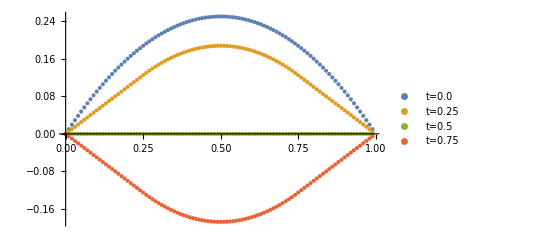

```mathematica
L=1.0;h=0.01;n=L/h;τ=0.01;
ListPlot[{plots⟦1;;n,2;;3⟧,plots⟦1+(n+1)*0.25/τ;;n+(n+1)*0.25/τ,2;;3⟧,plots⟦1+(n+1)*0.5/τ;;n+(n+1)*0.5/τ,2;;3⟧,plots⟦1+(n+1)*0.75/τ;;n+(n+1)*0.75/τ,2;;3⟧},PlotLegends->{"t=0.0","t=0.25","t=0.5","t=0.75"},PlotRange->All]
```

## Вариант 2

#### Численное решение

```mathematica
ClearAll["Global`*"]
NotebookDirectory[];
n = 2;
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Scheme_cross.txt"]],Table[Real,n+1]];
```

```mathematica
ListPlot3D[plots, PlotRange->All, AxesLabel->Automatic, ColorFunction->"Rainbow"]
```

-Graphics3D-

#### Эволюция во времени

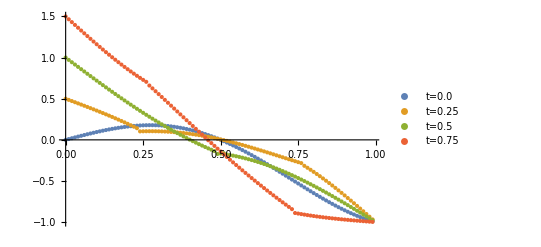

```mathematica
L=1.0;h=0.01;n=L/h;τ=0.01;
ListPlot[{plots⟦1;;n,2;;3⟧,plots⟦1+(n+1)*0.25/τ;;n+(n+1)*0.25/τ,2;;3⟧,plots⟦1+(n+1)*0.5/τ;;n+(n+1)*0.5/τ,2;;3⟧,plots⟦1+(n+1)*0.75/τ;;n+(n+1)*0.75/τ,2;;3⟧},PlotLegends->{"t=0.0","t=0.25","t=0.5","t=0.75"},PlotRange->All]
```

## Вариант 6

#### Численное решение

```mathematica
ClearAll["Global`*"]
NotebookDirectory[];
n = 2;
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Scheme_cross.txt"]],Table[Real,n+1]];
```

```mathematica
ListPlot3D[plots, PlotRange->All, AxesLabel->Automatic, ColorFunction->"Rainbow"]
```

-Graphics3D-

#### Эволюция во времени

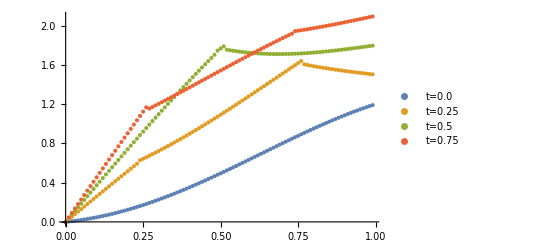

```mathematica
L=1.0;h=0.01;n=L/h;τ=0.01;
ListPlot[{plots⟦1;;n,2;;3⟧,plots⟦1+(n+1)*0.25/τ;;n+(n+1)*0.25/τ,2;;3⟧,plots⟦1+(n+1)*0.5/τ;;n+(n+1)*0.5/τ,2;;3⟧,plots⟦1+(n+1)*0.75/τ;;n+(n+1)*0.75/τ,2;;3⟧},PlotLegends->{"t=0.0","t=0.25","t=0.5","t=0.75"},PlotRange->All]
```

## Проверка порядков

```mathematica
ClearAll["`*"];
```

```mathematica
Sol[x_,t_]=Sin[π x]Cos[π t](*,{x,0,2},{t,0,1}*);
```

```mathematica
NotebookDirectory[];
n = 2;
For[i=1,i≤5,i++,len=0;
Subscript[plots, i]=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Scheme_cross_"<>ToString[2^i]<>".000000.txt"]],Table[Real,n+1]];
Subscript[Diff, i]= Table[Abs[Sol[Subscript[plots, i]⟦k⟧⟦2⟧,Subscript[plots, i]⟦k⟧⟦1⟧]-Subscript[plots, i]⟦k⟧⟦3⟧],{k,1,Length[Subscript[plots, i]]}];Subscript[Err, i] = Max[Subscript[Diff, i]];]
```

$Aborted

```mathematica
GridData=Join[{{"τ, h","AbsErr(τ, h)","Δ", "|log_qΔ|"}},Table[{{0.1 * (1/2)^(j-1),0.1*1/2^(j-1)},Subscript[Err, j],Subscript[Err, j]/Subscript[Err, j-1],-Log[Subscript[Err, j]/Subscript[Err, j-1]]/Log[2]},{j,1,5}]];
```

```mathematica
GridData⟦2⟧⟦3⟧=0;
GridData⟦2⟧⟦4⟧=0;
```

```mathematica
Grid[GridData,Frame->All]
```

τ, h | AbsErr(τ, h) | Δ | |log_qΔ|
{0.1,0.1} | 0.02 | 0 | 0
{0.05,0.05} | 0.005 | 0.250001 | 2.
{0.025,0.025} | 0.00125 | 0.25 | 2.
{0.0125,0.0125} | 0.000717853 | 0.574282 | 0.800169
{0.00625,0.00625} | 7.89533×10^-7 | 0.00109985 | 9.82847

## Закон сохранения энергии

```mathematica
ClearAll["Global`*"]
NotebookDirectory[];
n = 1;
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Energy.txt"]],Table[Real,n+1]];
```

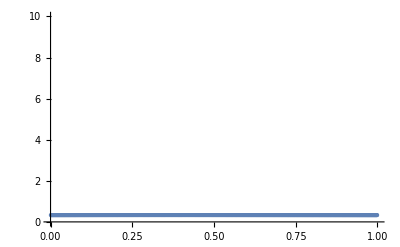

```mathematica
ListPlot[plots, PlotRange->{{0,1},{0,10}}, AxesLabel->Automatic, ColorFunction->"Rainbow"]
```

## Оценщик ошибок

```mathematica
ClearAll["`*"];
```

```mathematica
NotebookDirectory[];
n = 2;L=1.0 ;q=2;
For[i=1,i≤5,i++,
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Scheme_cross_"<>ToString[2^i]<>".000000.txt"]],Table[Real,n+1]];Subscript[h, i]=0.1/q^(i-1);Subscript[n, i]=L/Subscript[h, i];Subscript[τ, i]=0.1/q^(i-1);Subscript[plotsT, i]=plots⟦1+(Subscript[n, i]+1)*0.2/Subscript[τ, i];;Subscript[n, i]+(Subscript[n, i]+1)*0.2/Subscript[τ, i],2;;3⟧;(*при t=0.2*)
Subscript[pointNeed, i]=Max[Table[plots⟦j⟧[[3]],{j,1,Length[plots]}]](*Max[Table[Subscript[plotsT, i][[k]][[2]],{k,1,Length[Subscript[plotsT, i]]}]]*)(*Subscript[plotsT, i][[0.2/Subscript[h, i]+1]]*)(*при h=0.2*)]
```

```mathematica
Subscript[pointNeed, 5]
```

0.25

```mathematica
For[k=1,k<5,k++,Print[Subscript[Err, k]=Abs[Subscript[pointNeed, k+1]-Subscript[pointNeed, k]]]]
```

0.

0.

0.

«1 more identical outputs»

```mathematica
Subscript[Eitk, 2]=0;Subscript[Eitk, 1]=0;Subscript[Eitk, 3]=Subscript[Err, 2]/Subscript[Err, 1];Subscript[Eitk, 4]=Subscript[Err, 3]/Subscript[Err, 2];Subscript[Eitk, 5]=Subscript[Err, 4]/Subscript[Err, 3];
```

```mathematica
GridData=Join[{{"τ, h","AbsErr(τ, h)"}},Table[{{0.1 * (1/2)^(j-1),0.1*1/2^(j-1)},Subscript[Eitk, j]},{j,1,5}]];
```

```mathematica
GridData⟦2⟧⟦2⟧="-";
GridData⟦3⟧⟦2⟧="-";
```

```mathematica
Grid[GridData,Frame->All]
```

τ, h | AbsErr(τ, h)
{0.1,0.1} | -
{0.05,0.05} | -
{0.025,0.025} | 0.5
{0.0125,0.0125} | 0.5
{0.00625,0.00625} | 0.5